```mathematica
Quit[]
```

#### Kernels Control

```mathematica
LaunchKernels[8]
```

{KernelObject[1,local],KernelObject[2,local],KernelObject[3,local],KernelObject[4,local],KernelObject[5,local],KernelObject[6,local],KernelObject[7,local],KernelObject[8,local]}

```mathematica
CloseKernels[Kernels[]]
```

```mathematica
Kernels[]
```

### Main

#### Declaration

```mathematica
ParallelEvaluate[Off[General::stop]];
```

```mathematica
ParallelEvaluate[On[General::stop]];
```

```mathematica
If[$OperatingSystem=="Windows",{dir="D:/Documents/2-d-data";},{dir="~/Documents/2-d-data";}];
```

The amplitude

```mathematica
𝒞[expr_][ω1_,ω2_]:=ReplaceAll[expr,{ω1->ω2/(1+ω2-ω1),ω2->ω1/(1+ω2-ω1)}]
𝒫[expr_][ω1_,ω2_]:=ReplaceAll[expr,{ω1->(1+ω2-ω1)/ω2,ω2->1/ω2}]
ℛ[expr_][ω1_,ω2_]:=ReplaceAll[expr,{ω1->ω1/ω2,ω2->1/ω2}]
𝒮[expr_][ω1_,ω2_]:=ReplaceAll[expr,{ω1->1/ω1,ω2->(1+ω2-ω1)/ω1}]
```

```mathematica
EXPR[ω1_,ω2_][Ma_,Mb_,Mc_,Md_][ϕ1_,ϕ2_,ϕ3_,ϕ4_]=Through[Through[(ℳ0+𝒫[ℳ0[ω1,ω2]]+𝒞[ℳ0[ω1,ω2]]+ℛ[ℳ0[ω1,ω2]]+𝒫[𝒞[ℳ0[ω1,ω2]][ω1,ω2]]+ℛ[𝒞[ℳ0[ω1,ω2]][ω1,ω2]]+ℛ[𝒫[ℳ0[ω1,ω2]][ω1,ω2]]+ℛ[𝒫[𝒞[ℳ0[ω1,ω2]][ω1,ω2]][ω1,ω2]]+ℳ1[Ma,Mb,Mc,Md]+ℛ[ℳ1[Ma,Mb,Mc,Md][ω1,ω2]])[ω1,ω2]][ϕ1,ϕ2,ϕ3,ϕ4]];
```

```mathematica
ℳ0[ω1_,ω2_][ϕ1_,ϕ2_,ϕ3_,ϕ4_]:=If[ω2>ω1,4 g^2 ω1 NIntegrate[1/(y ω1-ω2-x)^2 ϕ1[(ω2-ω1+x)/(ω2-ω1+1)]ϕ2[y]ϕ3[x]ϕ4[(y ω1)/ω2],{x,0,1},{y,0,1}],0]
```

```mathematica
(*𝒞[f_Symbol[arg__]]:=f[#2/(1+#2-#1),#1/(1+#2-#1)]&[arg]
𝒫[f_Symbol[arg__]]:=f[(1+#2-#1)/#2,1/#2]&[arg]*)
```

```mathematica
ℳ1[Ma_,Mb_,Mc_,Md_][ω1_,ω2_][ϕ1_,ϕ2_,ϕ3_,ϕ4_]:=((#+𝒮[#][ω1,ω2])&[(*If[1>ω1,-4 g^2 NIntegrate[(ω1 ω2)/((y-1) ω1+(1-x)ω2)^2 ϕ1[(x ω2)/(1+ω2-ω1)]ϕ2[y]ϕ3[y ω1]ϕ4[x],{x,0,1},{y,0,1}],0]*)
If[1>ω1,-4 g^2(NIntegrate[(ω1 ω2)/((y-1) ω1+(1-x)ω2)^2 ϕ1[(x ω2)/(1+ω2-ω1)]ϕ2[y]ϕ3[y ω1]ϕ4[x],{x,0,1},{y,0,(ω1-ω2+x ω2)/ω1-λ}]+NIntegrate[(ω1 ω2)/((y-1) ω1+(1-x)ω2)^2 ϕ1[(x ω2)/(1+ω2-ω1)]ϕ2[y]ϕ3[y ω1]ϕ4[x],{x,0,1},{y,(ω1-ω2+x ω2)/ω1+λ,1}]-2/λ NIntegrate[ω2/ω1 ϕ1[(x ω2)/(1+ω2-ω1)]ϕ2[(ω1-ω2+x ω2)/ω1]ϕ3[((ω1-ω2+x ω2)/ω1 )ω1]ϕ4[x],{x,0,1}]),0]])+((#+𝒞[#][ω1,ω2])&[(*If[ω2>ω1,-4 g^2 NIntegrate[ω1/(y ω1-x)^2 ϕ1[(x+ω2-ω1)/(1+ω2-ω1)]ϕ2[y]ϕ3[x]ϕ4[((y-1) ω1+ω2)/ω2],{x,0,1},{y,0,1}],0]*)
If[ω2>ω1,-4 g^2(NIntegrate[ω1/(y ω1-x)^2 ϕ1[(x+ω2-ω1)/(1+ω2-ω1)]ϕ2[y]ϕ3[x]ϕ4[((y-1) ω1+ω2)/ω2],{x,0,1},{y,0,x/ω1-λ}]+NIntegrate[ω1/(y ω1-x)^2 ϕ1[(x+ω2-ω1)/(1+ω2-ω1)]ϕ2[y]ϕ3[x]ϕ4[((y-1) ω1+ω2)/ω2],{x,0,1},{y,x/ω1+λ,1}]-2/λ NIntegrate[1/ω1 ϕ1[(x+ω2-ω1)/(1+ω2-ω1)]ϕ2[x/ω1]ϕ3[x]ϕ4[((x/ω1-1) ω1+ω2)/ω2],{x,0,1}]),0]])+((#+𝒮[#][ω1,ω2]+𝒫[#][ω1,ω2]+𝒞[#][ω1,ω2])&[If[(ω2>ω1)&&(ω1>1),-(4 π)/Nc NIntegrate[(Mc^2+Md^2/ω2+Ma^2/(x-ω1)+Ma^2/(x-1)-Ma^2/(x-ω1+ω2)-Ma^2/x)ϕ1[(x-ω1+ω2)/(1+ω2-ω1)]ϕ2[x/ω1]ϕ3[x]ϕ4[(x-ω1+ω2)/ω2],{x,0,1}],0]])
```

```mathematica
ℳone[ω1_,ω2_][Ma_,Mb_,Mc_,Md_][ϕ1_,ϕ2_,ϕ3_,ϕ4_]:=EXPR[ω1,ω2][Ma,Mb,Mc,Md][ϕ1,ϕ2,ϕ3,ϕ4]
```

Solve ‘t Hooft equation

```mathematica
Clear[m1,m2,β,Nx]; (*β=1 unit*)
Nx=500;(*the size of the working matrix*)
β=1; (*the mass unit,definition β^2=g^2/(2Pi)Nc*)
(*m1=3.2*β;(*m1 and m2 are the bare masses of the quark and the anti-quark.*)
m2=3.2*β;*)
```

```mathematica
g=1;Nc=(β^2 π)/g^2;ℂ=0;(*ℂ denotes the interchange of final states.*)λ=10^-6;
```

```mathematica
vMatx[n_,m_]:=(vMatx[n-1,m-1] m/(m-1)+(8m)/(n+m-1)((1+(-1)^(n+m))/2))
vMatx[1,m_]:=4(1+(-1)^(m+1));
vMatx[n_,1]:=4/n(1+(-1)^(n+1));
```

```mathematica
Determineϕx[m1_,m2_,β_,Nx_]:=
Module[{HMatx,VMatx,vals,vecs,g,ϕx,ϕ},
SetSharedVariable[vecs,m1,m2,β,g];
SetSharedFunction[g];
HMatx=ParallelTable[4Min[n,m]((-1)^(n+m)(m1^2-β^2)+(m2^2-β^2)),{n,1,Nx},{m,1,Nx}];
VMatx=ParallelTable[vMatx[n,m],{n,1,Nx},{m,1,Nx}];
{vals,vecs}=Eigensystem[N[HMatx+VMatx]];
Do[g[j]=Dot[ParallelTable[Sin[i ArcCos[2x-1]],{i,1,Nx}],vecs[[j]]],{j,1,Nx}];
ϕx=ParallelTable[Quiet[g[Nx-n]/√NIntegrate[g[Nx-n]^2,{x,0,1}]],{n,0,20}];
Clear[g];
{√Reverse[vals] β,ϕx}
]
```

```mathematica
accDetermineϕ[m1_,m2_,β_,Nb_]:=
Module[{psi,ϵ=10^-6,Kernel1,Kernel2,hMT,sMT,sMatrix,hMTUp,hMT1,hMatrix,eg,vals,vecs,func,μ,nfunc},
Kernel1[n_][x_?NumberQ]:=NIntegrate[psi[n,y]/(x-y)^2,{y,0,x-ϵ}];
Kernel2[n_][x_?NumberQ]:=NIntegrate[psi[n,y]/(x-y)^2,{y,x+ϵ,1}];
psi[n_,x_]:=psi[n,x]=Which[n==0,x^(2-β)*(1-x)^β,n==1,(1-x)^(2-β)*x^β,n≥2,Sin[(n-1)*π*x]];
hMT[m_,n_]:=hMT[m,n]=NIntegrate[psi[m,x]((m1^2-1)/(x*(1-x))*psi[n,x]-Kernel1[n][x]-Kernel2[n][x]+(2psi[n,x])/ϵ),{x,ϵ,1-ϵ},WorkingPrecision->20];
sMT[m_,n_]:=sMT[m,n]=NIntegrate[psi[m,x]psi[n,x],{x,0,1}];
sMatrix=ParallelTable[Quiet[sMT[m,n]],{m,0,Nb},{n,0,Nb}]//Chop;hMTUp=PadLeft[#,Nb+1]&/@ParallelTable[Quiet[hMT[m,n]],{m,0,Nb},{n,m,Nb}];
(*Print[hMTUp];*)
hMatrix=Transpose[hMTUp]+hMTUp-DiagonalMatrix[Diagonal[hMTUp]];
(*Print[MatrixForm[hMatrix]];*)
eg[μ_]:=Det[hMatrix-μ^2*sMatrix];
μ=Sort@DeleteDuplicatesBy[Table[μ/.FindRoot[eg[μ]==0,{μ,a,a+0.2}],{a,0,Nb^2,0.2}],SetPrecision[#,2]&];
Print[μ];
vecs=(Flatten@NullSpace[hMatrix-#^2 sMatrix,Tolerance->0.001])&/@μ;
Print[vecs];Print[Dimensions@vecs];
func=ParallelTable[Table[psi[i,x],{i,0,Nb}].vecs[[j]],{j,1,Length[vecs]}];
nfunc=ParallelTable[Quiet[func[[n]]/√NIntegrate[func[[n]]^2,{x,0,1}]],{n,1,20}];
Clear[func,vecs];
{μ,nfunc}
]
```

```mathematica
ϕn[n_][ϕ_][x_]:=ϕ[x][[n+1]];
```

```mathematica
Mn[n_][vals_]:=vals[[n+1]];
```

Used z=(r_(2-))/(r_(1-)+r_(2-)), ω=(r_(4-))/(r_(1-)+r_(2-)), ω_1=(r_(2-))/(r_(3-)), ω_2=(r_(4-))/(r_(3-)) here.

```mathematica
ωfp[z_][M1_,M2_,M3_,M4_]:=(-√((M1^2 z-M2^2 z+M2^2+M3^2 z^2-M3^2 z-M4^2 z^2+M4^2 z)^2-4 (M4^2 z^2-M4^2 z) (M1^2 (-z)+M2^2 z-M2^2))+M1^2 (-z)+M2^2 z-M2^2-M3^2 z^2+M3^2 z+M4^2 z^2-M4^2 z)/(2 (M1^2 (-z)+M2^2 z-M2^2))(*transform z to ω (Barbon), solution 1.*)
```

```mathematica
ωfn[z_][M1_,M2_,M3_,M4_]:=(√((M1^2 z-M2^2 z+M2^2+M3^2 z^2-M3^2 z-M4^2 z^2+M4^2 z)^2-4 (M4^2 z^2-M4^2 z) (M1^2 (-z)+M2^2 z-M2^2))+M1^2 (-z)+M2^2 z-M2^2-M3^2 z^2+M3^2 z+M4^2 z^2-M4^2 z)/(2 (M1^2 (-z)+M2^2 z-M2^2))(*transform z to ω (Barbon), solution 2*)
```

```mathematica
ω2p[ω1_][M1_,M2_,M3_,M4_]:=1/(2 (M3^2 ω1-M2^2))(-√((M1^2 (-ω1)+M2^2 ω1-M2^2-M3^2 ω1^2+M3^2 ω1+M4^2 ω1)^2-4 (M4^2 ω1-M4^2 ω1^2) (M3^2 ω1-M2^2))+M1^2 ω1-M2^2 ω1+M2^2+M3^2 ω1^2-M3^2 ω1-M4^2 ω1)(*transform ω1 to ω2, your definition, solution 1*)
```

```mathematica
ω2n[ω1_][M1_,M2_,M3_,M4_]:=1/(2 (M3^2 ω1-M2^2))(√((M1^2 (-ω1)+M2^2 ω1-M2^2-M3^2 ω1^2+M3^2 ω1+M4^2 ω1)^2-4 (M4^2 ω1-M4^2 ω1^2) (M3^2 ω1-M2^2))+M1^2 ω1-M2^2 ω1+M2^2+M3^2 ω1^2-M3^2 ω1-M4^2 ω1);(*transform ω1 to ω2, your definition, solution 2*)
```

```mathematica
Sz[z_][M1_,M2_]:=M1^2/(1-z)+M2^2/z;(*Centre of mass energy*)
```

```mathematica
Sω1[ω1_][M1_,M2_,M3_,M4_]:=(M1^2/(1-ω1+ω2p[ω1][M1,M2,M3,M4])+M2^2/ω1)(1+ω2p[ω1][M1,M2,M3,M4]);
```

```mathematica
zfω1[ω1_][MA_,MB_,MC_,MD_]:=ω1/(1+ω2n[ω1][MA,MB,MC,MD])(*transform ω1 to z, using z=ω1/(1+ω2) and previous result of ω1 to ω2*)
ωfω1[ω1_][MA_,MB_,MC_,MD_]:=(ω2n[ω1][MA,MB,MC,MD])/(1+ω2n[ω1][MA,MB,MC,MD]);
```

```mathematica
ω1fz[z_][M1_,M2_,M3_,M4_]:=-z/(ωfp[z][M1,M2,M3,M4]-1);
ω2fz[z_][M1_,M2_,M3_,M4_]:=(-ωfp[z][M1,M2,M3,M4])/(ωfp[z][M1,M2,M3,M4]-1);(*transform z to ω1 and ω2, using z=ω1/(1+ω2) and previous result of z to ω*)
```

```mathematica
Msum[mQ_][n1_?IntegerQ,n2_?IntegerQ,n3_?IntegerQ,n4_?IntegerQ]:=
Module[{ϕxB,ΦB,ValsB,ϕxπ,Φπ,Valsπ,M1,M2,M3,ϕ1,ϕ2,ϕ3,Ares,filename,ωnow,m1,m2,M4,ϕ4,ω1,ω2,Sen,filenameacc,Determine},
(*SetSharedVariable[m2,m1];*)
m1=mQ;m2=mQ;
filename=If[m1==m2,"/eigenstate_m-"<>ToString[m1],"/eigenstate_m1-"<>ToString[m1]<>"_m2-"<>ToString[m2]]<>".wdx";
filenameacc=If[m1==m2,"/acceigenstate_m-"<>ToString[m1],"/acceigenstate_m1-"<>ToString[m1]<>"_m2-"<>ToString[m2]]<>".wdx";
If[FileNames[filenameacc,dir,Infinity]=={},If[ChoiceDialog["Choose to use BSW method or to use the original solution suggested by 't Hooft, ",{"Yes"->True,"No"->False}],Determine=Determineϕx,filename=filenameacc;Determine=accDetermineϕ]];
If[FileNames[filename,dir,Infinity]=={},
{
{ValsB,ϕxB}=Determine[m1,m2,β,Nx];
Set@@{ΦB[x_],ϕxB};
Export[dir<>filename,{ValsB,ϕxB}]
},
{
{ValsB,ϕxB}=Import[dir<>filename];
Set@@{ΦB[x_],ϕxB};
}
];
Print["Wavefunction build complete."];
(*Print[ϕn[#][ΦB][x]&[1]];*)
{M1,ϕ1}={Mn[#][ValsB],ϕn[#][ΦB]}&[n1];
{M2,ϕ2}={Mn[#][ValsB],ϕn[#][ΦB]}&[n2];
{M3,ϕ3}={Mn[#][ValsB],ϕn[#][ΦB]}&[n3];
{M4,ϕ4}={Mn[#][ValsB],ϕn[#][ΦB]}&[n4];
Print["M1=",M1,"  M2=",M2,"  M3=",M3,"  M4=",M4];
{{M1,M2,M3,M4},ParallelTable[ω2=ω2p[ω1][M1,M2,M3,M4];Sen=√(Sω1[ω1][M1,M2,M3,M4]);If[ω2∈Reals&&Sen∈Reals,
(*Print["ω1=",ω1,"    ω2=",ω2];*)(*it's for debug purpose, you can comment this*){Sen,ℳone[ω1,ω2][M1,M2,M3,M4][ϕ1,ϕ2,ϕ3,ϕ4]},Print["Overflow: ω1=",ω1]],{ω1,0.003,0.99,0.01}]}
]
```

#### Calc

```mathematica
Clear["Global`g$*"]
```

```mathematica
Information["Global`g$*"]
```

```mathematica
Clear[ϕx,m2,ϕ,vals,M1,M2,M3,ϕ1,ϕ2,ϕ3];
```

#### 2→2

The total amplitude (and the square):

Function structure is Msum[<one flavour quark mass>][(excited state)<1>,<2>,<3>,<4>]

```mathematica
Msumdat=Msum[60][0,0,0,0]
```

Wavefunction build complete.

M1=120.335  M2=120.335  M3=120.335  M4=120.335

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

{{120.335,120.335,120.335,120.335},{{2203.6,1.54872×10^-10},{1069.13,3.12786×10^-9},{811.717,1.05248×10^-8},{684.284,2.32489×10^-8},{605.262,4.25152×10^-8},{550.406,6.96439×10^-8},{509.631,1.06361×10^-7},{477.894,1.54228×10^-7},{452.358,2.15012×10^-7},{431.292,2.92086×10^-7},{413.571,3.88097×10^-7},{398.427,5.06437×10^-7},{385.319,6.52252×10^-7},{373.85,8.21556×10^-7},{363.723,1.03251×10^-6},{354.713,1.28632×10^-6},{346.64,1.59047×10^-6},{339.366,1.95423×10^-6},{332.776,2.38867×10^-6},{326.779,2.90314×10^-6},{321.3,3.51077×10^-6},{316.274,4.29679×10^-6},{311.65,5.1742×10^-6},{307.382,6.21244×10^-6},{303.432,7.44943×10^-6},{299.767,8.71372×10^-6},{296.359,0.0000103807},{293.184,0.0000126838},{290.219,0.000015115},{287.447,0.0000180256},{284.85,0.000021386},{282.414,0.0000254185},{280.125,0.0000302103},{277.972,0.0000358956},{275.945,0.00004266},{274.033,0.0000507249},{272.23,0.0000603816},{270.526,0.0000718375},{268.915,0.0000855938},{267.392,0.000102085},{265.949,0.000121858},{264.582,0.000145707},{263.286,0.000174462},{262.057,0.000208331},{260.89,0.00025147},{259.782,0.000302482},{258.73,0.000364975},{257.73,0.000441511},{256.78,0.000535264},{255.876,0.000650482},{255.016,0.000794416},{254.199,0.000970663},{253.421,0.00119218},{252.68,0.00148367},{251.976,0.00181998},{251.305,0.00225797},{250.667,0.00280946},{250.06,0.00353119},{249.482,0.00445115},{248.932,0.00564611},{248.409,0.00713188},{247.912,0.00921288},{247.439,0.0120301},{246.989,0.0155878},{246.561,0.0205026},{246.155,0.0272556},{245.77,0.0365279},{245.404,0.0494595},{245.057,0.0683539},{244.728,0.0960355},{244.416,0.137731},{244.121,0.202308},{243.842,0.305527},{243.579,0.473672},{243.33,0.756517},{243.096,1.24998},{242.875,2.1121},{242.668,3.60691},{242.473,6.351},{242.291,11.2155},{242.12,19.7633},{241.961,34.547},{241.813,59.5979},{241.676,99.794},{241.549,167.075},{241.431,274.229},{241.324,431.462},{241.226,660.731},{241.137,980.679},{241.056,967.641},{240.984,1960.36},{240.92,2589.03},{240.864,3415.6},{240.815,4323.},{240.774,5273.2},{240.74,6216.79},{240.713,7115.6},{240.693,7831.87},{240.679,8328.26}}}

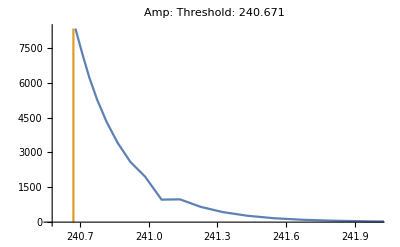

```mathematica
ListPlot[{Select[Re@Msumdat[[2]],#∈Reals&],{{Msumdat[[1,1]]+Msumdat[[1,2]],0},{Msumdat[[1,1]]+Msumdat[[1,2]],Last[Msumdat[[2]]][[2]]}}},PlotRange->{{Msumdat[[1,1]]+Msumdat[[1,2]]-0.1,242},All},Joined->True,PlotLabel->"Amp: Threshold: "<>ToString[Msumdat[[1,1]]+Msumdat[[1,2]]]]
```

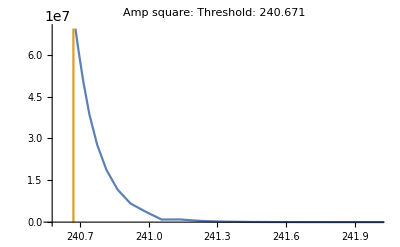

```mathematica
ListPlot[{Transpose@{Transpose[Msumdat[[2]]][[1]],(Transpose[Msumdat[[2]]][[2]])^2},{{Msumdat[[1,1]]+Msumdat[[1,2]],0},{Msumdat[[1,1]]+Msumdat[[1,2]],(Last[Msumdat[[2]]][[2]])^2}}},PlotRange->{{Msumdat[[1,1]]+Msumdat[[1,2]]-0.1,242},All},Joined->True,PlotLabel->"Amp square: Threshold: "<>ToString[Msumdat[[1,1]]+Msumdat[[1,2]]]]
```

### Debug

```mathematica
Block[{mQ=60},m1=mQ;m2=mQ;
filename=If[m1==m2,"/eigenstate_m-"<>ToString[m1],"/eigenstate_m1-"<>ToString[m1]<>"_m2-"<>ToString[m2]]<>".wdx";
filenameacc=If[m1==m2,"/acceigenstate_m-"<>ToString[m1],"/acceigenstate_m1-"<>ToString[m1]<>"_m2-"<>ToString[m2]]<>".wdx";
If[FileNames[filenameacc,dir,Infinity]=={},If[ChoiceDialog["Choose to use BSW method or not"],Determine=Determineϕx,filename=filenameacc;Determine=accDetermineϕ]];
If[FileNames[filename,dir,Infinity]=={},
{
{ValsB,ϕxB}=Determine[m1,m2,β,Nx];
Set@@{ΦB[x_],ϕxB};
Export[dir<>filename,{ValsB,ϕxB}]
},
{
{ValsB,ϕxB}=Import[dir<>filename];
Set@@{ΦB[x_],ϕxB};
}
];
Print["Wavefunction build complete."];
(*Print[ϕn[#][ΦB][x]&[1]];*)
{M1,ϕ1}={Mn[#][ValsB],ϕn[#][ΦB]}&[0];
{M2,ϕ2}={Mn[#][ValsB],ϕn[#][ΦB]}&[0];
{M3,ϕ3}={Mn[#][ValsB],ϕn[#][ΦB]}&[0];
{M4,ϕ4}={Mn[#][ValsB],ϕn[#][ΦB]}&[0];]
```

Wavefunction build complete.

```mathematica
ParallelTable[ℳ1[M1,M2,M3,M4][ω1,ω2p[ω1][M1,M2,M3,M4]][ϕ1,ϕ2,ϕ3,ϕ4],{ω1,0.1,0.9,0.1}]
```

{3.57115×10^-7,3.31587×10^-6,0.0000202997,0.000115472,0.000746744,0.0066131,0.118411,16.65,1778.83}

```mathematica
ParallelTable[ℳ1[M1,M2,M3,M4][ω1/(ω2p[ω1][M1,M2,M3,M4]),1/(ω2p[ω1][M1,M2,M3,M4])][ϕ1,ϕ2,ϕ3,ϕ4],{ω1,0.1,0.9,0.1}]
```

{3.57115×10^-7,3.31586×10^-6,0.0000202997,0.000115472,0.000746742,0.00661315,0.118411,16.65,1778.83}

```mathematica
ℳ1[Ma,Mb,Mc,Md][ω1,ω2][ϕ1,ϕ2,ϕ3,ϕ4]
```

If[1/ω2>(1-ω1+ω2)/ω2&&(1-ω1+ω2)/ω2>1,-1/Nc(4 π) NIntegrate[(Mc^2+Md^2/(1/ω2)+Ma^2/(x-(1-ω1+ω2)/ω2)+Ma^2/(x-1)-Ma^2/(x-(1-ω1+ω2)/ω2+1/ω2)-Ma^2/x) ϕ1[(x-(1-ω1+ω2)/ω2+1/ω2)/(1+1/ω2-(1-ω1+ω2)/ω2)] ϕ2[x/((1-ω1+ω2)/ω2)] ϕ3[x] ϕ4[(x-(1-ω1+ω2)/ω2+1/ω2)/(1/ω2)],{x,0,1}],0]+If[ω2>ω1&&ω1>1,-((4 π) NIntegrate[(Mc^2+Md^2/ω2+Ma^2/(x-ω1)+Ma^2/(x-1)-Ma^2/(x-ω1+ω2)-Ma^2/x) ϕ1[(x-ω1+ω2)/(1+ω2-ω1)] ϕ2[x/ω1] ϕ3[x] ϕ4[(x-ω1+ω2)/ω2],{x,0,1}])/Nc,0]+If[ω1/(1-ω1+ω2)>ω2/(1-ω1+ω2)&&ω2/(1-ω1+ω2)>1,-1/Nc(4 π) NIntegrate[(Mc^2+Md^2/(ω1/(1-ω1+ω2))+Ma^2/(x-ω2/(1-ω1+ω2))+Ma^2/(x-1)-Ma^2/(x-ω2/(1-ω1+ω2)+ω1/(1-ω1+ω2))-Ma^2/x) ϕ1[(x-ω2/(1-ω1+ω2)+ω1/(1-ω1+ω2))/(1+ω1/(1-ω1+ω2)-ω2/(1-ω1+ω2))] ϕ2[x/(ω2/(1-ω1+ω2))] ϕ3[x] ϕ4[(x-ω2/(1-ω1+ω2)+ω1/(1-ω1+ω2))/(ω1/(1-ω1+ω2))],{x,0,1}],0]+If[(1-ω1+ω2)/ω1>1/ω1&&1/ω1>1,-1/Nc(4 π) NIntegrate[(Mc^2+Md^2/((1-ω1+ω2)/ω1)+Ma^2/(x-1/ω1)+Ma^2/(x-1)-Ma^2/(x-1/ω1+(1-ω1+ω2)/ω1)-Ma^2/x) ϕ1[(x-1/ω1+(1-ω1+ω2)/ω1)/(1+(1-ω1+ω2)/ω1-1/ω1)] ϕ2[x/(1/ω1)] ϕ3[x] ϕ4[(x-1/ω1+(1-ω1+ω2)/ω1)/((1-ω1+ω2)/ω1)],{x,0,1}],0]+If[1>1/ω1,-4 g^2 (NIntegrate[((1-ω1+ω2) ϕ1[(x (1-ω1+ω2))/(ω1 (1+(1-ω1+ω2)/ω1-1/ω1))] ϕ2[y] ϕ3[y/ω1] ϕ4[x])/(ω1 ω1 ((y-1)/ω1+((1-x) (1-ω1+ω2))/ω1)^2),{x,0,1},{y,0,(1/ω1-(1-ω1+ω2)/ω1+(x (1-ω1+ω2))/ω1)/(1/ω1)-λ}]+NIntegrate[((1-ω1+ω2) ϕ1[(x (1-ω1+ω2))/(ω1 (1+(1-ω1+ω2)/ω1-1/ω1))] ϕ2[y] ϕ3[y/ω1] ϕ4[x])/(ω1 ω1 ((y-1)/ω1+((1-x) (1-ω1+ω2))/ω1)^2),{x,0,1},{y,(1/ω1-(1-ω1+ω2)/ω1+(x (1-ω1+ω2))/ω1)/(1/ω1)+λ,1}]-(2 NIntegrate[((1-ω1+ω2) ϕ1[(x (1-ω1+ω2))/(ω1 (1+(1-ω1+ω2)/ω1-1/ω1))] ϕ2[(1/ω1-(1-ω1+ω2)/ω1+(x (1-ω1+ω2))/ω1)/(1/ω1)] ϕ3[(1/ω1-(1-ω1+ω2)/ω1+(x (1-ω1+ω2))/ω1)/(ω1/ω1)] ϕ4[x])/(ω1/ω1),{x,0,1}])/λ),0]+If[1>ω1,-4 g^2 (NIntegrate[((ω1 ω2) ϕ1[(x ω2)/(1+ω2-ω1)] ϕ2[y] ϕ3[y ω1] ϕ4[x])/((y-1) ω1+(1-x) ω2)^2,{x,0,1},{y,0,(ω1-ω2+x ω2)/ω1-λ}]+NIntegrate[((ω1 ω2) ϕ1[(x ω2)/(1+ω2-ω1)] ϕ2[y] ϕ3[y ω1] ϕ4[x])/((y-1) ω1+(1-x) ω2)^2,{x,0,1},{y,(ω1-ω2+x ω2)/ω1+λ,1}]-(2 NIntegrate[(ω2 ϕ1[(x ω2)/(1+ω2-ω1)] ϕ2[(ω1-ω2+x ω2)/ω1] ϕ3[((ω1-ω2+x ω2) ω1)/ω1] ϕ4[x])/ω1,{x,0,1}])/λ),0]+If[ω2>ω1,-4 g^2 (NIntegrate[(ω1 ϕ1[(x+ω2-ω1)/(1+ω2-ω1)] ϕ2[y] ϕ3[x] ϕ4[((y-1) ω1+ω2)/ω2])/(y ω1-x)^2,{x,0,1},{y,0,x/ω1-λ}]+NIntegrate[(ω1 ϕ1[(x+ω2-ω1)/(1+ω2-ω1)] ϕ2[y] ϕ3[x] ϕ4[((y-1) ω1+ω2)/ω2])/(y ω1-x)^2,{x,0,1},{y,x/ω1+λ,1}]-(2 NIntegrate[(ϕ1[(x+ω2-ω1)/(1+ω2-ω1)] ϕ2[x/ω1] ϕ3[x] ϕ4[((x/ω1-1) ω1+ω2)/ω2])/ω1,{x,0,1}])/λ),0]+If[ω1/(1-ω1+ω2)>ω2/(1-ω1+ω2),-4 g^2 (NIntegrate[(ω2 ϕ1[(x+ω1/(1-ω1+ω2)-ω2/(1-ω1+ω2))/(1+ω1/(1-ω1+ω2)-ω2/(1-ω1+ω2))] ϕ2[y] ϕ3[x] ϕ4[(((y-1) ω2)/(1-ω1+ω2)+ω1/(1-ω1+ω2))/(ω1/(1-ω1+ω2))])/((1-ω1+ω2) ((y ω2)/(1-ω1+ω2)-x)^2),{x,0,1},{y,0,x/(ω2/(1-ω1+ω2))-λ}]+NIntegrate[(ω2 ϕ1[(x+ω1/(1-ω1+ω2)-ω2/(1-ω1+ω2))/(1+ω1/(1-ω1+ω2)-ω2/(1-ω1+ω2))] ϕ2[y] ϕ3[x] ϕ4[(((y-1) ω2)/(1-ω1+ω2)+ω1/(1-ω1+ω2))/(ω1/(1-ω1+ω2))])/((1-ω1+ω2) ((y ω2)/(1-ω1+ω2)-x)^2),{x,0,1},{y,x/(ω2/(1-ω1+ω2))+λ,1}]-(2 NIntegrate[(ϕ1[(x+ω1/(1-ω1+ω2)-ω2/(1-ω1+ω2))/(1+ω1/(1-ω1+ω2)-ω2/(1-ω1+ω2))] ϕ2[x/(ω2/(1-ω1+ω2))] ϕ3[x] ϕ4[(((x/(ω2/(1-ω1+ω2))-1) ω2)/(1-ω1+ω2)+ω1/(1-ω1+ω2))/(ω1/(1-ω1+ω2))])/(ω2/(1-ω1+ω2)),{x,0,1}])/λ),0]

```mathematica
ℳ1[Ma,Mb,Mc,Md][ω1/ω2,1/ω2][ϕ1,ϕ2,ϕ3,ϕ4]
```

If[1/ω2>ω1/ω2&&ω1/ω2>1,-((4 π) NIntegrate[(Mc^2+Md^2/(1/ω2)+Ma^2/(x-ω1/ω2)+Ma^2/(x-1)-Ma^2/(x-ω1/ω2+1/ω2)-Ma^2/x) ϕ1[(x-ω1/ω2+1/ω2)/(1+1/ω2-ω1/ω2)] ϕ2[x/(ω1/ω2)] ϕ3[x] ϕ4[(x-ω1/ω2+1/ω2)/(1/ω2)],{x,0,1}])/Nc,0]+If[ω1/((1+1/ω2-ω1/ω2) ω2)>1/((1+1/ω2-ω1/ω2) ω2)&&1/((1+1/ω2-ω1/ω2) ω2)>1,-1/Nc(4 π) NIntegrate[(Mc^2+Md^2/(ω1/((1+1/ω2-ω1/ω2) ω2))+Ma^2/(x-1/((1+1/ω2-ω1/ω2) ω2))+Ma^2/(x-1)-Ma^2/(x-1/((1+1/ω2-ω1/ω2) ω2)+ω1/((1+1/ω2-ω1/ω2) ω2))-Ma^2/x) ϕ1[(x-1/((1+1/ω2-ω1/ω2) ω2)+ω1/((1+1/ω2-ω1/ω2) ω2))/(1+ω1/((1+1/ω2-ω1/ω2) ω2)-1/((1+1/ω2-ω1/ω2) ω2))] ϕ2[x/(1/((1+1/ω2-ω1/ω2) ω2))] ϕ3[x] ϕ4[(x-1/((1+1/ω2-ω1/ω2) ω2)+ω1/((1+1/ω2-ω1/ω2) ω2))/(ω1/((1+1/ω2-ω1/ω2) ω2))],{x,0,1}],0]+If[ω2>(1+1/ω2-ω1/ω2) ω2&&(1+1/ω2-ω1/ω2) ω2>1,-1/Nc(4 π) NIntegrate[(Mc^2+Md^2/ω2+Ma^2/(x-(1+1/ω2-ω1/ω2) ω2)+Ma^2/(x-1)-Ma^2/(x-(1+1/ω2-ω1/ω2) ω2+ω2)-Ma^2/x) ϕ1[(x-(1+1/ω2-ω1/ω2) ω2+ω2)/(1+ω2-(1+1/ω2-ω1/ω2) ω2)] ϕ2[x/((1+1/ω2-ω1/ω2) ω2)] ϕ3[x] ϕ4[(x-(1+1/ω2-ω1/ω2) ω2+ω2)/ω2],{x,0,1}],0]+If[((1+1/ω2-ω1/ω2) ω2)/ω1>ω2/ω1&&ω2/ω1>1,-1/Nc(4 π) NIntegrate[(Mc^2+Md^2/(((1+1/ω2-ω1/ω2) ω2)/ω1)+Ma^2/(x-ω2/ω1)+Ma^2/(x-1)-Ma^2/(x-ω2/ω1+((1+1/ω2-ω1/ω2) ω2)/ω1)-Ma^2/x) ϕ1[(x-ω2/ω1+((1+1/ω2-ω1/ω2) ω2)/ω1)/(1+((1+1/ω2-ω1/ω2) ω2)/ω1-ω2/ω1)] ϕ2[x/(ω2/ω1)] ϕ3[x] ϕ4[(x-ω2/ω1+((1+1/ω2-ω1/ω2) ω2)/ω1)/(((1+1/ω2-ω1/ω2) ω2)/ω1)],{x,0,1}],0]+If[1>ω1/ω2,-4 g^2 (NIntegrate[(ω1 ϕ1[x/(ω2 (1+1/ω2-ω1/ω2))] ϕ2[y] ϕ3[(y ω1)/ω2] ϕ4[x])/(ω2 ω2 (((y-1) ω1)/ω2+(1-x)/ω2)^2),{x,0,1},{y,0,(ω1/ω2-1/ω2+x/ω2)/(ω1/ω2)-λ}]+NIntegrate[(ω1 ϕ1[x/(ω2 (1+1/ω2-ω1/ω2))] ϕ2[y] ϕ3[(y ω1)/ω2] ϕ4[x])/(ω2 ω2 (((y-1) ω1)/ω2+(1-x)/ω2)^2),{x,0,1},{y,(ω1/ω2-1/ω2+x/ω2)/(ω1/ω2)+λ,1}]-(2 NIntegrate[(ϕ1[x/(ω2 (1+1/ω2-ω1/ω2))] ϕ2[(ω1/ω2-1/ω2+x/ω2)/(ω1/ω2)] ϕ3[((ω1/ω2-1/ω2+x/ω2) ω1)/((ω1 ω2)/ω2)] ϕ4[x])/((ω2 ω1)/ω2),{x,0,1}])/λ),0]+If[1>ω2/ω1,-4 g^2 (NIntegrate[((ω2 ((1+1/ω2-ω1/ω2) ω2)) ϕ1[(x ((1+1/ω2-ω1/ω2) ω2))/(ω1 (1+((1+1/ω2-ω1/ω2) ω2)/ω1-ω2/ω1))] ϕ2[y] ϕ3[(y ω2)/ω1] ϕ4[x])/(ω1 ω1 (((y-1) ω2)/ω1+((1-x) ((1+1/ω2-ω1/ω2) ω2))/ω1)^2),{x,0,1},{y,0,(ω2/ω1-((1+1/ω2-ω1/ω2) ω2)/ω1+(x ((1+1/ω2-ω1/ω2) ω2))/ω1)/(ω2/ω1)-λ}]+NIntegrate[((ω2 ((1+1/ω2-ω1/ω2) ω2)) ϕ1[(x ((1+1/ω2-ω1/ω2) ω2))/(ω1 (1+((1+1/ω2-ω1/ω2) ω2)/ω1-ω2/ω1))] ϕ2[y] ϕ3[(y ω2)/ω1] ϕ4[x])/(ω1 ω1 (((y-1) ω2)/ω1+((1-x) ((1+1/ω2-ω1/ω2) ω2))/ω1)^2),{x,0,1},{y,(ω2/ω1-((1+1/ω2-ω1/ω2) ω2)/ω1+(x ((1+1/ω2-ω1/ω2) ω2))/ω1)/(ω2/ω1)+λ,1}]-1/λ 2 NIntegrate[1/((ω1 ω2)/ω1)((1+1/ω2-ω1/ω2) ω2) ϕ1[(x ((1+1/ω2-ω1/ω2) ω2))/(ω1 (1+((1+1/ω2-ω1/ω2) ω2)/ω1-ω2/ω1))] ϕ2[(ω2/ω1-((1+1/ω2-ω1/ω2) ω2)/ω1+(x ((1+1/ω2-ω1/ω2) ω2))/ω1)/(ω2/ω1)] ϕ3[((ω2/ω1-((1+1/ω2-ω1/ω2) ω2)/ω1+(x ((1+1/ω2-ω1/ω2) ω2))/ω1) ω2)/((ω2 ω1)/ω1)] ϕ4[x],{x,0,1}]),0]+If[1/ω2>ω1/ω2,-4 g^2 (NIntegrate[(ω1 ϕ1[(x+1/ω2-ω1/ω2)/(1+1/ω2-ω1/ω2)] ϕ2[y] ϕ3[x] ϕ4[(((y-1) ω1)/ω2+1/ω2)/(1/ω2)])/(ω2 ((y ω1)/ω2-x)^2),{x,0,1},{y,0,x/(ω1/ω2)-λ}]+NIntegrate[(ω1 ϕ1[(x+1/ω2-ω1/ω2)/(1+1/ω2-ω1/ω2)] ϕ2[y] ϕ3[x] ϕ4[(((y-1) ω1)/ω2+1/ω2)/(1/ω2)])/(ω2 ((y ω1)/ω2-x)^2),{x,0,1},{y,x/(ω1/ω2)+λ,1}]-(2 NIntegrate[(ϕ1[(x+1/ω2-ω1/ω2)/(1+1/ω2-ω1/ω2)] ϕ2[x/(ω1/ω2)] ϕ3[x] ϕ4[(((x/(ω1/ω2)-1) ω1)/ω2+1/ω2)/(1/ω2)])/(ω1/ω2),{x,0,1}])/λ),0]+If[ω1/((1+1/ω2-ω1/ω2) ω2)>1/((1+1/ω2-ω1/ω2) ω2),-4 g^2 (NIntegrate[(ϕ1[(x+ω1/((1+1/ω2-ω1/ω2) ω2)-1/((1+1/ω2-ω1/ω2) ω2))/(1+ω1/((1+1/ω2-ω1/ω2) ω2)-1/((1+1/ω2-ω1/ω2) ω2))] ϕ2[y] ϕ3[x] ϕ4[((y-1)/((1+1/ω2-ω1/ω2) ω2)+ω1/((1+1/ω2-ω1/ω2) ω2))/(ω1/((1+1/ω2-ω1/ω2) ω2))])/(((1+1/ω2-ω1/ω2) ω2) (y/((1+1/ω2-ω1/ω2) ω2)-x)^2),{x,0,1},{y,0,x/(1/((1+1/ω2-ω1/ω2) ω2))-λ}]+NIntegrate[(ϕ1[(x+ω1/((1+1/ω2-ω1/ω2) ω2)-1/((1+1/ω2-ω1/ω2) ω2))/(1+ω1/((1+1/ω2-ω1/ω2) ω2)-1/((1+1/ω2-ω1/ω2) ω2))] ϕ2[y] ϕ3[x] ϕ4[((y-1)/((1+1/ω2-ω1/ω2) ω2)+ω1/((1+1/ω2-ω1/ω2) ω2))/(ω1/((1+1/ω2-ω1/ω2) ω2))])/(((1+1/ω2-ω1/ω2) ω2) (y/((1+1/ω2-ω1/ω2) ω2)-x)^2),{x,0,1},{y,x/(1/((1+1/ω2-ω1/ω2) ω2))+λ,1}]-(2 NIntegrate[(ϕ1[(x+ω1/((1+1/ω2-ω1/ω2) ω2)-1/((1+1/ω2-ω1/ω2) ω2))/(1+ω1/((1+1/ω2-ω1/ω2) ω2)-1/((1+1/ω2-ω1/ω2) ω2))] ϕ2[x/(1/((1+1/ω2-ω1/ω2) ω2))] ϕ3[x] ϕ4[((x/(1/((1+1/ω2-ω1/ω2) ω2))-1)/((1+1/ω2-ω1/ω2) ω2)+ω1/((1+1/ω2-ω1/ω2) ω2))/(ω1/((1+1/ω2-ω1/ω2) ω2))])/(1/((1+1/ω2-ω1/ω2) ω2)),{x,0,1}])/λ),0]

```mathematica
?EXPR
```

Global`EXPR

EXPR[ω1_,ω2_][Ma_,Mb_,Mc_,Md_][ϕ1_,ϕ2_,ϕ3_,ϕ4_]=ℳ0[ω1,ω2][ϕ1,ϕ2,ϕ3,ϕ4]+ℳ0[ω1/ω2,1/ω2][ϕ1,ϕ2,ϕ3,ϕ4]+ℳ0[1/((1+1/ω2-ω1/ω2) ω2),ω1/((1+1/ω2-ω1/ω2) ω2)][ϕ1,ϕ2,ϕ3,ϕ4]+ℳ0[(1+1/ω2-ω1/ω2) ω2,ω2][ϕ1,ϕ2,ϕ3,ϕ4]+ℳ0[ω2/(1-ω1+ω2),ω1/(1-ω1+ω2)][ϕ1,ϕ2,ϕ3,ϕ4]+ℳ0[(1-ω1+ω2)/ω2,1/ω2][ϕ1,ϕ2,ϕ3,ϕ4]+ℳ0[ω2/(1+ω2-(1+1/ω2-ω1/ω2) ω2),((1+1/ω2-ω1/ω2) ω2)/(1+ω2-(1+1/ω2-ω1/ω2) ω2)][ϕ1,ϕ2,ϕ3,ϕ4]+ℳ0[1/(ω2 (1+1/ω2-(1-ω1+ω2)/ω2)),(1-ω1+ω2)/(ω2 (1+1/ω2-(1-ω1+ω2)/ω2))][ϕ1,ϕ2,ϕ3,ϕ4]+ℳ1[Ma,Mb,Mc,Md][ω1,ω2][ϕ1,ϕ2,ϕ3,ϕ4]+ℳ1[Ma,Mb,Mc,Md][ω1/ω2,1/ω2][ϕ1,ϕ2,ϕ3,ϕ4]

```mathematica
FindRoot[√(Sω1[ω1][M1,M2,M3,M4])==241.137,{ω1,0.9,0.99}]
```

{ω1→0.882942}

```mathematica
Reduce[1/(ω2p[ω1][M1,M2,M3,M4])>(1-ω1+ω2p[ω1][M1,M2,M3,M4])/(ω2p[ω1][M1,M2,M3,M4])&&(1-ω1+ω2p[ω1][M1,M2,M3,M4])/(ω2p[ω1][M1,M2,M3,M4])>1,ω1]
```

$Aborted

```mathematica
Block[{ω1,ω2},ω2=ω2n[ω1][M1,M2,M3,M4]; ω1/.FindInstance[1/ω2>(1-ω1+ω2)/ω2&&(1-ω1+ω2)/ω2>1&&0<ω1<1,ω1,100]]
```

ω1

```mathematica
Block[{ω1,ω2},ω2=ω2n[ω1][M1,M2,M3,M4]; ω1/.FindInstance[ω2>ω1&&ω1>1&&0<ω1<1,ω1,100]]
```

ω1

```mathematica
Block[{ω1,ω2},ω2=ω2n[ω1][M1,M2,M3,M4]; ω1/.FindInstance[(1-ω1+ω2)/ω1>1/ω1&&1/ω1>1&&0<ω1<1,ω1,100]]
```

ω1

```mathematica
ω1/.FindInstance[ω2p[ω1][M1,M2,M3,M4]>ω1&&ω1>1&&0<ω1<1,ω1,100]
```

ω1

```mathematica
Block[{ω1=0.1,ω2},ω2=ω2n[ω1][M1,M2,M3,M4]; Print[1/ω2>(1-ω1+ω2n[ω1][M1,M2,M3,M4])/(ω2n[ω1][M1,M2,M3,M4])&&(1-ω1+ω2n[ω1][M1,M2,M3,M4])/(ω2n[ω1][M1,M2,M3,M4])>1&&0<ω1<1];NIntegrate[(M3^2+M4^2/(ω1/(1-ω1+ω2))+M1^2/(x-ω2/(1-ω1+ω2))+M1^2/(x-1)-M1^2/(x-ω2/(1-ω1+ω2)+ω1/(1-ω1+ω2))-M1^2/x) ϕ1[(x-ω2/(1-ω1+ω2)+ω1/(1-ω1+ω2))/(1+ω1/(1-ω1+ω2)-ω2/(1-ω1+ω2))] ϕ2[x/(ω2/(1-ω1+ω2))] ϕ3[x] ϕ4[(x-ω2/(1-ω1+ω2)+ω1/(1-ω1+ω2))/(ω1/(1-ω1+ω2))],{x,0,1}]]
```

False

8.83407707562666×10^916

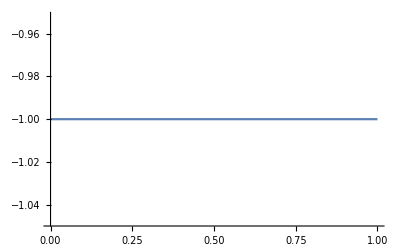

```mathematica
Plot[ω2n[ω1][M1,M2,M3,M4],{ω1,0,1}]
```

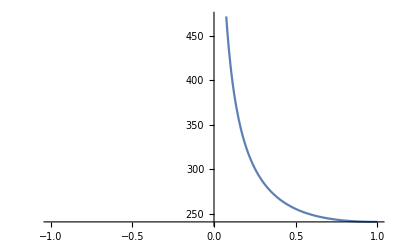

```mathematica
Plot[√(Sω1[ω1][M1,M2,M3,M4]),{ω1,-1,1}]
```

```mathematica
Block[{ω1=0.8829424796893336,ω2},ω2=ω2p[ω1][M1,M2,M3,M4];ℳone[ω1,ω2][M1][ϕ1,ϕ2,ϕ3,ϕ4]]
```

1955.93

```mathematica
Block[{ω1=0.907479105147823,ω2,Sen},ω2=ω2p[ω1][M1,M2,M3,M4];Sen=√(Sω1[ω1][M1,M2,M3,M4]);If[ω2∈Reals&&Sen∈Reals,Print["ω1=",ω1,"    ω2=",ω2];{Sen,ℳone[ω1,ω2][M1][ϕ1,ϕ2,ϕ3,ϕ4]},Print["Overflow: ω1=",ω1]]]
```

ω1=0.907479    ω2=0.708776

NIntegrate::ncvb: 在接近 {x,y} = {0.47396,0.589163} 处的 x 中进行 18 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 7087.77 和 143060..

NIntegrate::ncvb: 在接近 {x,y} = {0.526042,0.410879} 处的 x 中进行 18 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 7087.77 和 143060..

{244.244,-113404.}

```mathematica
Block[{ω1=0.907479105147823,ω2},ω2=ω2p[ω1][M1,M2,M3,M4];𝒞[ℳ0[ω1,ω2]][ω1,ω2][ϕ1,ϕ2,ϕ3,ϕ4]]
```

0.09278

```mathematica
Block[{ω1=0.907479105147823,ω2},ω2=ω2p[ω1][M1,M2,M3,M4];ℳ1[M1][ω1,ω2][ϕ1,ϕ2,ϕ3,ϕ4]]
```

NIntegrate::slwcon: 数值积分收敛速度太慢；可能是如下原因：奇点，积分值是 0，高度振荡的被积函数，或者 WorkingPrecision 太小.

NIntegrate::ncvb: 在接近 {x,y} = {0.99972774468308135838688632812676360117620788514614105224609375,9.83724×10^-6} 处的 y 中进行 18 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 4.33383×10^258 和 8.91081×10^258.

-3.46707×10^259

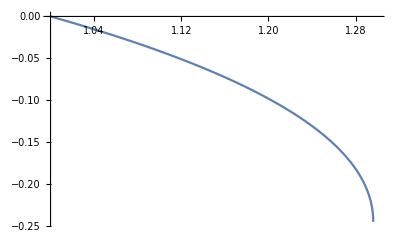

```mathematica
Plot[(ω2p[ω1][M1,M2,M3,M4])/ω1,{ω1,1,1.3}]
```

```mathematica
Block[{ω1=0.907479105147823,ω2},ω2=ω2p[ω1][M1,M2,M3,M4];NIntegrate[ω1/(y ω1-x)^2 ϕ1[(x+ω2-ω1)/(1+ω2-ω1)]ϕ2[y]ϕ3[x]ϕ4[((y-1) ω1+ω2)/ω2],{x,0,1},{y,0,1}]]
```

NIntegrate::slwcon: 数值积分收敛速度太慢；可能是如下原因：奇点，积分值是 0，高度振荡的被积函数，或者 WorkingPrecision 太小.

NIntegrate::ncvb: 在接近 {x,y} = {0.429446,0.907482} 处的 y 中进行 18 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 -9.1960468217209363414030970359671991396517715069998422535022594849×10^1780+6.6644443576245410010334590115150447725581246899922275744416000763×10^1767 ⅈ 和 2.8418655168893182884967858465873180630766840277546920593796254944×10^1780.

-9.19604682172094×10^1780+6.7×10^1767 ⅈ

```mathematica
Block[{ω1=0.907479105147823,ω2},ω2=ω2p[ω1][M1,M2,M3,M4];NIntegrate[ω1/(y ω1-x)^2 ϕ1[(x+ω2-ω1)/(1+ω2-ω1)]ϕ2[y]ϕ3[x]ϕ4[((y-1) ω1+ω2)/ω2],{x,0,1},{y,0,x/ω1-λ}]+NIntegrate[ω1/(y ω1-x)^2 ϕ1[(x+ω2-ω1)/(1+ω2-ω1)]ϕ2[y]ϕ3[x]ϕ4[((y-1) ω1+ω2)/ω2],{x,0,1},{y,x/ω1+λ,1}]-2/λ NIntegrate[1/ω1 ϕ1[(x+ω2-ω1)/(1+ω2-ω1)]ϕ2[x/ω1]ϕ3[x]ϕ4[((x/ω1-1) ω1+ω2)/ω2],{x,0,1}]]
```

NIntegrate::slwcon: 数值积分收敛速度太慢；可能是如下原因：奇点，积分值是 0，高度振荡的被积函数，或者 WorkingPrecision 太小.

NIntegrate::ncvb: 在接近 {x,y} = {0.99972774468308135838688632812676360117620788514614105224609375,9.83724×10^-6} 处的 y 中进行 18 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 4.33383×10^258 和 8.91081×10^258.

4.33383×10^258

```mathematica
NI1[ω1_,ω2_][x_?NumberQ]:=NIntegrate[(ω1 ω2)/((y-1) ω1+(1-x)ω2)^2 ϕ1[(x ω2)/(1+ω2-ω1)]ϕ2[y]ϕ3[y ω1]ϕ4[x],{y,0,(ω1-ω2+x ω2)/ω1-λ}]
NI2[ω1_,ω2_][x_?NumberQ]:=NIntegrate[(ω1 ω2)/((y-1) ω1+(1-x)ω2)^2 ϕ1[(x ω2)/(1+ω2-ω1)]ϕ2[y]ϕ3[y ω1]ϕ4[x],{y,(ω1-ω2+x ω2)/ω1+λ,1}]
```

```mathematica
λ=10^-4;
```

```mathematica
Block[{ω1=0.907479105147823,ω2},ω2=ω2p[ω1][M1,M2,M3,M4];-4 g^2(NIntegrate[NI1[ω1,ω2][x],{x,0,1}]+NIntegrate[NI2[ω1,ω2][x],{x,0,1}]-2/λ NIntegrate[ω1 ω2 ϕ1[(x ω2)/(1+ω2-ω1)]ϕ2[(ω1-ω2+x ω2)/ω1]ϕ3[((ω1-ω2+x ω2)/ω1 )ω1]ϕ4[x],{x,0,1}])]
```

$Aborted

```mathematica
Table[Block[{ω1=0.3,ω2},ω2=ω2p[ω1][M1,M2,M3,M4];-4 g^2(NIntegrate[1/(y-x)^2 ϕ1[x ω2]ϕ2[y]ϕ3[y ω1]ϕ4[x],{x,λ,1-λ},{y,0,x-λ}]+NIntegrate[1/(y-x)^2 ϕ1[x ω2]ϕ2[y]ϕ3[y ω1]ϕ4[x],{x,λ,1-λ},{y,x+λ,1}]-2/λ NIntegrate[ ϕ1[x ω2]ϕ2[x]ϕ3[x ω1]ϕ4[x],{x,λ,1-λ}])],{λ,Table[10^-m,{m,2,7,1}]}]
```

{19.4562,19.7495,19.7852,19.7698,19.711,19.3019}